```mathematica
v=V/n;
```

```mathematica
P=R*T/(v-b)-a/v^2
```

-(a n^2)/V^2+(R T)/(-b+V/n)

```mathematica
D[P,V]
```

(2 a n^2)/V^3-(R T)/(n (-b+V/n)^2)

```mathematica
D[D[P,V],V]
```

-(6 a n^2)/V^4+(2 R T)/(n^2 (-b+V/n)^3)

```mathematica
R*T=(P+a/(9*b^2))*(3*b-b)
```

Set::write: Tag Times in R T is Protected.

2 b (a/(9 b^2)-(a n^2)/V^2+(R T)/(-b+V/n))

```mathematica
Simplify[2*a/(9*b^2*V)-((P+a/(9*b^2))*(3*b-b))/(2*b)^2]
```

(a (-1/b+(9 b n^2)/V^2+4/V)+(9 b n R T)/(b n-V))/(18 b^2)

```mathematica
(3*b*n-b*n)^2
```

4 b^2 n^2

## Problem 3

```mathematica
Expand[(p+3/v1^2)*(3*v1-1)]
```

-p-3/v1^2+9/v1+3 p v1

```mathematica
t=1.1;
```

```mathematica
p=(8*t+3/v1^2-9/v1)/(-1+3*v1);
```

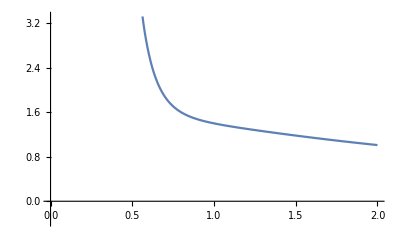

```mathematica
Plot[p,{v1,0,2}]
```